```mathematica
(*
Characteristic polynomial of the system in closed loop with a PDmu controller
*)
```

```mathematica
Δ[s_,kp_,kd_,μ_]:= s^2+Sqrt[s+2]+(s+1)(kp+kd s^μ)
```

```mathematica
(*
Stability crossing curve for w = 0
*)
```

```mathematica
Solve[Δ[0, kp, kd, μ]==0, kp]
```

{{kp→-√2-0^μ kd}}

```mathematica
(*
Computing kp(w) and kd(w)
*)
```

```mathematica
FullSimplify[Solve[ComplexExpand[Re[Δ[I*w,kp,kd,mu]]==0 && ComplexExpand[Im[Δ[I*w,kp,kd,mu]]]==0],{kp,kd}]]
```

{{kp→-((-√(w^4)^(mu/2) (w^2-(4+w^2)^(1/4) Cos[(1/2) Arg[2+ⅈ w]]) (w Cos[mu Arg[ⅈ w]]+Sin[mu Arg[ⅈ w]])+(w^2)^(mu/2) (4+w^2)^(1/4) Sin[(1/2) Arg[2+ⅈ w]] (-Cos[mu Arg[ⅈ w]]+w Sin[mu Arg[ⅈ w]]))/(w (-(w^2)^(mu/2)+√(w^4)^(mu/2)) Cos[mu Arg[ⅈ w]]+((w^2)^(1+mu/2)+√(w^4)^(mu/2)) Sin[mu Arg[ⅈ w]])),kd→(-w^3+(4+w^2)^(1/4) (w Cos[(1/2) Arg[2+ⅈ w]]-Sin[(1/2) Arg[2+ⅈ w]]))/(w (-(w^2)^(mu/2)+√(w^4)^(mu/2)) Cos[mu Arg[ⅈ w]]+((w^2)^(1+mu/2)+√(w^4)^(mu/2)) Sin[mu Arg[ⅈ w]])}}

```mathematica
kpp[w_, mu_]:=-(-√((w^4)^(mu/2)) (w^2-(4+w^2)^(1/4) Cos[1/2 Arg[2+ⅈ w]]) (w Cos[mu Arg[ⅈ w]]+Sin[mu Arg[ⅈ w]])+(w^2)^(mu/2) (4+w^2)^(1/4) Sin[1/2 Arg[2+ⅈ w]] (-Cos[mu Arg[ⅈ w]]+w Sin[mu Arg[ⅈ w]]))/(w (-(w^2)^(mu/2)+√((w^4)^(mu/2))) Cos[mu Arg[ⅈ w]]+((w^2)^(1+mu/2)+√((w^4)^(mu/2))) Sin[mu Arg[ⅈ w]])
```

```mathematica
kdd[w_, mu_]:=(-w^3+(4+w^2)^(1/4) (w Cos[1/2 Arg[2+ⅈ w]]-Sin[1/2 Arg[2+ⅈ w]]))/(w (-(w^2)^(mu/2)+√((w^4)^(mu/2))) Cos[mu Arg[ⅈ w]]+((w^2)^(1+mu/2)+√((w^4)^(mu/2))) Sin[mu Arg[ⅈ w]])
```

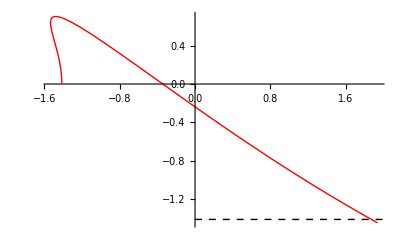

```mathematica
P1 =ParametricPlot[{kpp[w, 0.5], kdd[w, 0.5]}, {w, 0, 2.4}, PlotStyle->{Red, Thick}];
P2 = Plot[-Sqrt[2],{kd0, 0, 10}, PlotStyle->{Black,  Dashed, Thick} ];
Show[P1, P2]
```

```mathematica
SetDirectory[NotebookDirectory[]];
<<ToMatlab.m
f=OpenWrite["funciones.m"];
WriteMatlab[kpp[w, mu],f,"kp"];
WriteMatlab[kdd[w, mu],f,"kd"];
Close[f];
```